# Nodes have a limited capacity and they receive packages according to a probability function.

```mathematica
NotebookDirectory[]
```

/home/jovillal/redes/

```mathematica
$HistoryLength=0;
```

Represent a graph as a list of it nodes, each node a list {m_j,{n_j1,n_j2,…,n_jN_j}}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,…,n_jN} the list of neighbors of node m.
When ω_(j k)==0 or Sin[ω_(j k) t+ϕ_(j k)]≥ 0 marbles can leave the node, here ω_(j k) is a frequency, and ϕ_(j k) is a phase associated to the link that connects nodes j and k.
All nodes have a fixed capacity K, a node may have more than K packages at a given time according to prob[m_(j,t),δ_(j,t),Tmp].
Given a network, the rules of the simulation are that at every tick:
	■ A subset of nodes is selected with probability np, the subset is selected according to weights that are proportional to its outdegree (nodes with larger outdegree are more likely to be chosen).
	◼ Every node in the subset tries to pass one of its marbles to one of its neighbors (chosen randomly). 
	■ A marble is passed if ω_(j k)==0∨Sin[ω_(j k) t+ϕ_(j k)]≥ 0, otherwise the marble stays. 
	■ A node receives all incoming marbles at with probability prob[m_(j,t),δ_(j,t),Tmp] , where m_(j,t) is the amount of marbles at the node, δ_(j,t) is the total incoming marbles from adjacent nodes, and Tmp is an external parameter.

## Functions

## Auxiliaries

eCR[m, i,j] takes a matrix m and exchanges columns and rows i and j.

```mathematica
eCR[am_?MatrixQ,column_Integer,row_Integer]:=Block[{ret=am},
ret[[{column,row}]]=ret[[{row,column}]];
{ret[[All,column]],ret[[All,row]]}={ret[[All,row]],ret[[All,column]]};
ret]
```

sortByOut[m] takes an adjacency matrix and sorts it in a way that VertexOutDegree[AdjacencyGrapg[sortByOut[m]]] is sorted from greater to less, this is equivalent to saying that the first node has the highest out degree and the last node has the smallest.

```mathematica
sortByOut[am_?MatrixQ/;Length[am]==Length[Transpose[am]]]:=Module[
{out=Total/@am,new=am,i,ex},
Do[
If[out[[i]]<Max[out[[i+1;;-1]]],
new=eCR[new,i,i+FirstPosition[out[[i+1;;-1]],Max[out[[i+1;;-1]]]][[1]]];
out=Total/@new;]
,{i,Length[am]-1}];
new
];
sortByOut[_]:=Print["sortByOut input is not a matrix or a square matrix."]
```

sortByIn[m] takes an adjacency matrix and sorts it in a way that VertexInDegree[AdjacencyGrapg[sortByIn[m]]] is sorted from greater to less, this is equivalent to saying that the first node has the highest in degree and the last node has the smallest.

```mathematica
sortByIn[am_?MatrixQ/;Length[am]==Length[Transpose[am]]]:=Module[
{in=Total/@Transpose[am],new=am,i,ex},
Do[
If[in[[i]]<Max[in[[i+1;;-1]]],
new=eCR[new,i,i+FirstPosition[in[[i+1;;-1]],Max[in[[i+1;;-1]]]][[1]]];
in=Total/@Transpose[new];]
,{i,Length[am]-1}];
new
];
sortByIn[_]:=Print["sortByIn input is not a matrix or a square matrix."]
```

remove[g,subset] takes a graph g as  defined by graphToNet and a list of lists of integers subset that gives the number of nodes that are supposed to donate one marble.
It returns a set of pairs {rs_i,b_i} where rs_i==subset[[i]] and b_i=0 if node rs_i can’t donate or b∈{M} indicates the receiving node.

```mathematica
remove[g_,subset_List]:=Module[{},
(*Print[subset];*)
Table[If[g[[i,2]]≠{}&&g[[i,1]]!={},{i,RandomChoice[g[[i,2]]]},{i,0}],{i,subset}]
]
```

add[g,out] takes a graph g as  defined by graphToNet, and list of integers out (output from remove). It returns a set of lists {{δ_i,r_i}}  where δ_i is the set of marbles that arrive at node i, and r_i the set of packages that exit node i.

```mathematica
add[g_List,{}]:=ConstantArray[{{},{}},M];
add[g_List,{{_,0}}]:=ConstantArray[{{},{}},M];
add[g_List,out_List/;Length[out]==1]:=Module[{r=ConstantArray[{},M],δ=ConstantArray[{},M]},
(*build the r*)
r=ReplacePart[r,out[[1,1]]->{g[[out[[1,1]],1,1]]}];
(*now build the δ*)
δ=ReplacePart[δ,out[[1,2]]->{g[[out[[1,1]],1,1]]}];
Transpose[{δ,r}]
];
add[g_List,out_List/;out[[2,All]]==ConstantArray[0,Length[out]]]:=ConstantArray[{{},{}},M];
add[g_List,out_List/;Length[out]==M]:=Module[{ct,pct,rem=out,i},
ct=Count[out[[All,2]],#]&/@Range[M] (*Number of packages each node will receive*);
(*Print[ct];*)
(*pct=Table[Boole[RandomReal[]<=prob[Length[graph[[i,1]]],ct[[i]],Tmp]],{i,M}]*)
(*This is 0 or 1 depending on the probability of recieving*);
(*Print[pct];*)
(*pct=ct*pct (*now pct has the accurate number of packages that every node will recieve*);*)
(*Print[pct];*)
(*Modify out with the accurate number of packages*)
(*For[i=1,i<=M,i++,
If[ct[[i]]!=pct[[i]],
rem=ReplacePart[rem,Thread[Rule[Cases[Position[rem,ct[[i]]],{_,2}],0]]]
]
];*)
(*now build the r*)
ct=Table[If[rem[[i,2]]!=0,{g[[i,1]][[1]]},{}],{i,M}];
(*Print["This is r ",ct];*)
(*now build the δ*)
pct=Table[With[{x=Position[rem[[All,2]],i]},
If[x=={},{},
Table[g[[j,1]][[1]],{j,Flatten[x]}]
]],{i,M}];
(*Print["This is δ ",pct];*)
Transpose[{pct,ct}]
];
add[g_List,out_List/;1<Length[out]<M]:=Module[{ct,r,donors,δ=ConstantArray[{},M],i},
ct=Count[out[[All,2]],#]&/@Range[M] (*Number of packages each node will receive*);
donors=Cases[out,{x_,j_/;j>0}->x];
(*Print["This is ct ",ct];
Print["This is donors ",donors];*)
(*now build the r*)
r=Table[If[MemberQ[donors,i],{g[[i,1]][[1]]},{}],{i,M}];
(*Print["This is r ",r];*)
(*now build the δ*)
For[i=1,i<=M,i++,
If[ct[[i]]!=0,
δ[[i]]=Table[g[[out[[j,1]],1,1]],{j,Flatten[Position[out[[All,2]],i]]}]]
];
(*Print["This is δ ",δ];*)
Transpose[{δ,r}]
];
```

updateGraph[g, a] takes a graph g and a list of pairs a={{δ_i,r_i}} (output from add), and returns and updated version of g consistent with a.

```mathematica
updateGraph[g_List,a_List/;a==ConstantArray[{{},{}},M]]:=g;
updateGraph[g_List,a_List]:=Module[{packs=g[[All,1]]},
packs=Table[Drop[packs[[i]],Length[a[[i,2]]]],{i,M}];
packs=Table[Flatten[Append[packs[[i]],a[[i,1]]]],{i,M}];
Transpose[{packs,g[[All,2]]}]
];
```

fillWith[marbles] takes an integer and returns an array of size M with a list of integers m_i at position i, such that ∑_i Length[m_i]==marbles and Length[m_i]≃Length[m_j] for all places.

```mathematica
fillWith[marbles_Integer]:=Module[{int=Floor[marbles/M],float=Mod[marbles,M],ret,count=1},
ret=RandomSample[ConstantArray[int,M]+Join[ConstantArray[1,float],ConstantArray[0,M-float]]];
Table[If[ret[[i]]==0,{},count=count+ret[[i]];Range[count-ret[[i]],count-1]],{i,M}]
]
```

padTally[l, n] takes a list of pairs ordered by the first element and returns a list of length n of the form {{0,p_0},{1,p_1},…,{n-1,p_(n-1)}} where p_i=0 or p_i==l[[j,2]] if l[[j,1]]==i+1.

```mathematica
padTally[l_,n_]:=l/;Length[l]≥n;
padTally[l_,n_]:=Block[{ret},
ret=ReplacePart[ConstantArray[0,n],MapThread[Rule,{l[[All,1]]+1,l[[All,2]]}]];
{Range[n]-1,ret}//Transpose
];
```

## Probability function

prob[m,δ,Tmp] gives the probability that a node with m packages would receive δ incoming packages.

```mathematica
prob[m_Integer,δ_Integer,0]:=Piecewise[{{1,m+δ<=K}}];
prob[m_Integer,δ_Integer,Tmp_?NumberQ]:=(1+Exp[-K/Tmp])/(1+Exp[(m+δ-K)/Tmp]);
```

```mathematica
Limit[(1+Exp[-S/x])/(1+Exp[(δ-S)/x]),x->0,Assumptions->S>0&&δ-S>0,Direction->"FromAbove"]
```

0

```mathematica
Limit[(1+Exp[-S/x])/(1+Exp[(δ-S)/x]),x->0,Assumptions->S>0&&δ-S>0,Direction->"FromBelow"]
```

∞

```mathematica
Manipulate[Show[Plot[(1+Exp[-K/Tmp])/(1+Exp[(x-K)/Tmp]),{x,0,30},PlotRange->{0,1.1},AxesLabel->{"m_j+δ","P(recieve)"}],Graphics[{Red,Line[{{K,0},{K,1}}]}]],
{Tmp,.001,.1},
{K,0,10}]
```

General::munfl: Exp[-7020.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7019.39] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Integrate[1/(ⅇ^(-K/Tmp) (1+ⅇ^(K/Tmp)) Tmp Log[1+ⅇ^(K/Tmp)])(1+Exp[-K/Tmp])/(1+Exp[(x-K)/Tmp]),{x,0,∞}]
```

ConditionalExpression[1, Re[Tmp]>0]

## Main functions

graphToNet[graph, ini,order] takes a graph (Mathematica style) and returns a list of elements {{m_i},{n_(j 1),n_(j 2),…,n_(j N_j)}}; with {m_i} the set of packages in the node, and j∈{1,…, N} (N the number of nodes in the graph), n_(j s) the s-th outer neighbour of node j.  The elements are ordered by default according to their outdegree (the first node has the biggest outdegree).
ini can be one of the following:
	• an integer a, will put a marbles on each node.
	• a list of two integers {a,n}, this would put a marbles on node n and no marbles on the other nodes.
	• a list of integers of length N that represents the initial distribution of marbles
order is optional, it determines the order of the elements according to their the out degree 
	• if order is omitted or order≡"Out"  (or whatever else) elements are ordered according to their outdegree (the first node has the biggest outdegree).
	• if order≡"In"  elements are ordered according to their indegree (the first node has the biggest indegree).

```mathematica
graphToNet[g_Graph,ini_Integer]:=Module[{nei},
nei=sortByOut[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
Transpose[{Partition[Range[ini VertexCount[g]],ini],nei}]
];
graphToNet[g_Graph,ini:{a_,n_}]:=Module[{nei},
nei=sortByOut[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
ReplacePart[{{},#}&/@nei,{n,1}->Range[a]]
];
graphToNet[g_Graph,ini_List]:=Module[{nei},
nei=sortByOut[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
Transpose[{ini,nei}]
]/;Length[ini]==VertexCount[g];
graphToNet[g_Graph,ini:{a_,n_},"Out"]:=graphToNet[g,{a,n}];
graphToNet[g_Graph,ini_List,"Out"]:=graphToNet[g,ini];
graphToNet[g_Graph,ini:{a_,n_},"In"]:=Module[{nei},
nei=sortByIn[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
ReplacePart[{{},#}&/@nei,{n,1}->Range[a]]
];
graphToNet[g_Graph,ini_List,"In"]:=Module[{nei},
nei=sortByIn[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
Transpose[{ini,nei}]
]/;Length[ini]==VertexCount[g];
```

netEvolve[graph,T] takes a graph (represented as previously described), with M nodes,  and implements the rule described above for T ticks, there is no maximum number of marbles per node. It returns a list E where every element represents the state of the graph at time t. For each time t, there are M elements that contain the marbles present in each node. This is E[[t,m]] gives a list with the marbles present at time t in node m.
This version assumes ω_(j k)=ϕ_(j k)=0

```mathematica
netEvolve[graph_List,T_Integer]:=NestList[updateGraph[#,add[#,remove[#,Range[M]]]]&,graph,T]
```

netEvolve[graph,P,T] takes a graph (represented as previously described), with N nodes, and two integers 1<=P<N and T, and implements the rule described above for T ticks. P defines the number of nodes that deliver one package per tick. It returns a list E where every element represents the state of the graph at time t. For each time t, there are N elements that contain the marbles present in each node. This is E[[t,m]] gives a list with the marbles present at time t in node m.
This version assumes ω_(j k)=ϕ_(j k)=0

```mathematica
netEvolve[graph_List,M,T_Integer]:=netEvolve[graph,T];
netEvolve[graph_List,P_Integer/;1<=P<M,T_Integer]:=Module[{subset},
subset:=Sort[RandomSample[Range[M],P]];
NestList[updateGraph[#,add[#,remove[#,subset]]]&,graph,T]
]
```

difCoef[mrb, evol, net] takes a group of marbles mrb, the evolution of a network evol (as produced by netEvol), and a network net (as produced by  graphToNet) and calculates the diffusion coefficient for each pair of marbles in mrb. It returns a linear model for each par of coefficients, assuming that, once on a relaxed state, two marbles in the same node drift apart ∝β t^h (the linear model is of the form h x).

```mathematica
difCoef[{m1_Int}|{},evol_List,net_List]:={};
difCoef[pairs:{m1_Int,m2_Int_},evol_List,net_List]:=Module[{distances},
distances=distanceBetween[pairs,evol,net];
LinearModelFit[Transpose[{Log[Range[2,Length[#]]],Log[Rest[#]+1]}],x,x,IncludeConstantBasis->False]&/@distances
];
difCoef[mrb_List,evol_List,net_List]:=Module[{distances,pairs=Cases[Permutations[mrb,{2}],{x_,y_}/;x<y]},
distances=distanceBetween[#,evol,net]&/@pairs;
LinearModelFit[Transpose[{Log[Range[2,Length[#]]],Log[Rest[#]+1]}],x,x,IncludeConstantBasis->False]&/@distances
];
```

## Simulations --PHYSICAL REVIEW E 92, 012103 (2015)

### 2 nodes

```mathematica
twonodes={{0,1},{1,0}};
```

```mathematica
M=Length[twonodes]
```

2

```mathematica
NN=10;
```



```mathematica
AdjacencyGraph[twonodes]
```

```mathematica
twonodes=graphToNet[AdjacencyGraph[twonodes],{NN,1}];
```

```mathematica
tmpall=netEvolve[twonodes,1000 NN];
```

```mathematica
tmp1=netEvolve[twonodes,1,1000 NN];
```

```mathematica
tmpall=Transpose[Table[Length/@tmpall[[i]][[All,1]],{i,Length[tmpall]}]];
```

```mathematica
tmp1=Transpose[Table[Length/@tmp1[[i]][[All,1]],{i,Length[tmp1]}]];
```

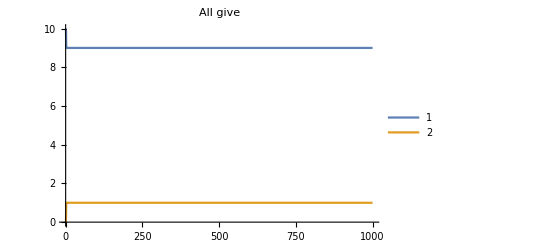

```mathematica
ListLinePlot[tmpall[[All,1;;1000]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"All give"]
```

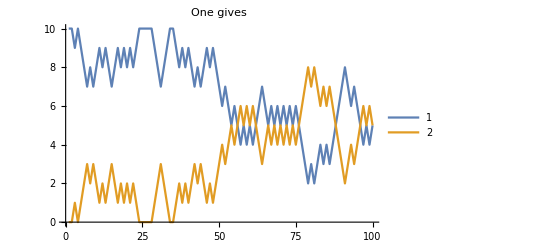

```mathematica
ListLinePlot[tmp1[[All,1;;100]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"One gives"]
```

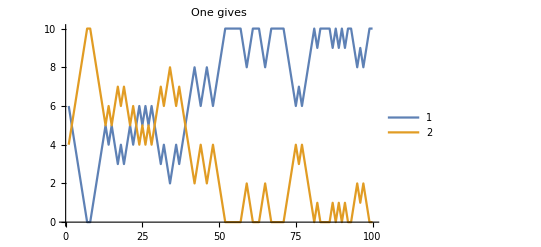

```mathematica
ListLinePlot[tmp1[[All,-100;;-1]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"One gives"]
```

#### Averages

```mathematica
lots=Table[netEvolve[twonodes,1000 NN],{100}];
```

```mathematica
lots=Table[Transpose[Table[Length/@lots[[j]][[i]][[All,1]],{i,Length[lots[[j]]]}]],{j,Length[lots]}];
```

```mathematica
lotsmd=Table[Table[Around[Transpose[lots[[All,n]]][[i]]],{n,2}],{i,1,1000NN,100}];
```

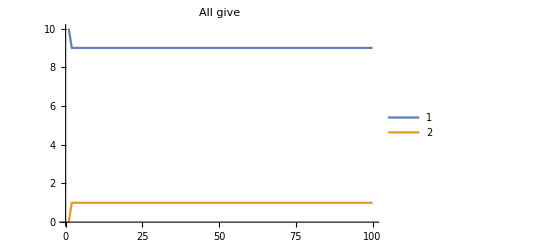

```mathematica
ListLinePlot[Transpose[lotsmd],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"All give"]
```

```mathematica
lots1=Table[netEvolve[twonodes,1,1000 NN],{100}];
```

```mathematica
lots1=Table[Transpose[Table[Length/@lots1[[j]][[i]][[All,1]],{i,Length[lots1[[j]]]}]],{j,Length[lots1]}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,2}],{i,1,1000NN,100}];
```

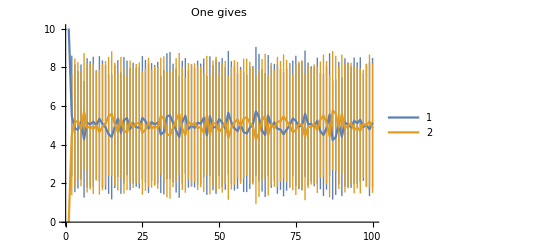

```mathematica
ListLinePlot[Transpose[lots1md],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"One gives"]
```

### Directed triangle

```mathematica
triangle={{0,1,1},{1,0,0},{0,1,0}};
```

```mathematica
M=Length[triangle]
```

3

```mathematica
NN=10;
```

```mathematica
AdjacencyGraph[triangle]
```

-Graphics-

```mathematica
Δ=graphToNet[AdjacencyGraph[triangle],{NN,1}];
```

```mathematica
tmpall=netEvolve[Δ,1000 NN];
```

```mathematica
tmp2=netEvolve[Δ,2,1000 NN];
```

```mathematica
tmp1=netEvolve[Δ,1,1000 NN];
```

```mathematica
tmpall=Transpose[Table[Length/@tmpall[[i]][[All,1]],{i,Length[tmpall]}]];
tmp2=Transpose[Table[Length/@tmp2[[i]][[All,1]],{i,Length[tmp2]}]];
tmp1=Transpose[Table[Length/@tmp1[[i]][[All,1]],{i,Length[tmp1]}]];
```

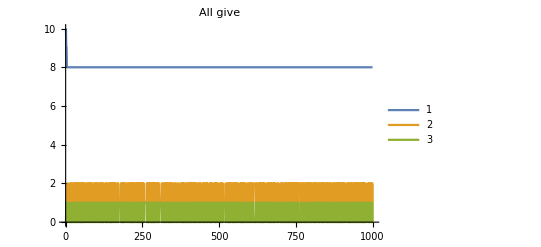

```mathematica
ListLinePlot[tmpall[[All,1;;1000]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"All give"]
```

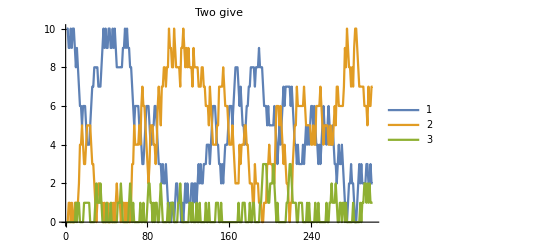

```mathematica
ListLinePlot[tmp2[[All,1;;300]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"Two give"]
```

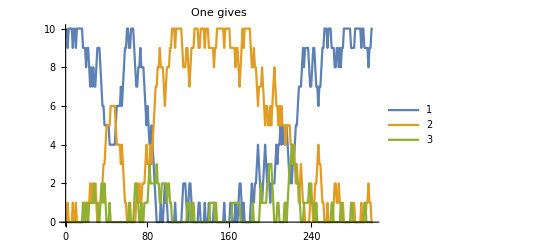

```mathematica
ListLinePlot[tmp1[[All,1;;300]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"One gives"]
```

#### Averages

```mathematica
lots=Table[netEvolve[Δ,1000 NN],{100}];
```

```mathematica
lots=Table[Transpose[Table[Length/@lots[[j]][[i]][[All,1]],{i,Length[lots[[j]]]}]],{j,Length[lots]}];
```

```mathematica
lotsmd=Table[Table[Around[Transpose[lots[[All,n]]][[i]]],{n,3}],{i,1,1000NN,100}];
```

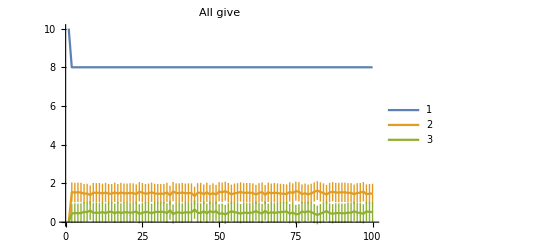

```mathematica
ListLinePlot[Transpose[lotsmd],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"All give"]
```

```mathematica
lots2=Table[netEvolve[Δ,2,1000 NN],{100}];
```

```mathematica
lots2=Table[Transpose[Table[Length/@lots2[[j]][[i]][[All,1]],{i,Length[lots2[[j]]]}]],{j,Length[lots2]}];
```

```mathematica
lotsmd=Table[Table[Around[Transpose[lots2[[All,n]]][[i]]],{n,3}],{i,1,1000NN,100}];
```

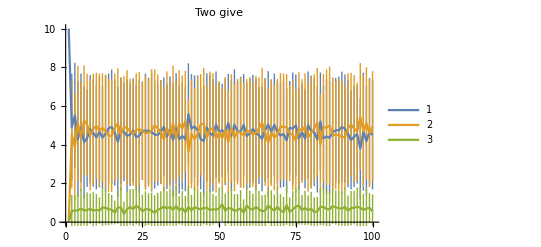

```mathematica
ListLinePlot[Transpose[lotsmd],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"Two give
"]
```

```mathematica
lots1=Table[netEvolve[Δ,1,1000 NN],{100}];
```

```mathematica
lots1=Table[Transpose[Table[Length/@lots1[[j]][[i]][[All,1]],{i,Length[lots1[[j]]]}]],{j,Length[lots1]}];
```

```mathematica
lotsmd=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,3}],{i,1,1000NN,100}];
```

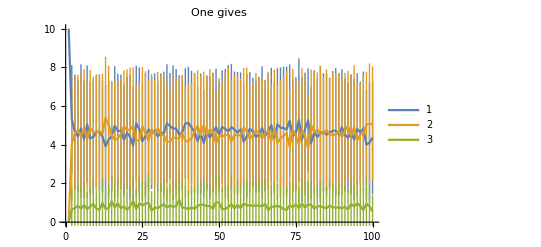

```mathematica
ListLinePlot[Transpose[lotsmd],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"One gives"]
```

### Non-directed triangle

```mathematica
ndtriangle={{0,1,1},{1,0,1},{1,1,0}};
```

```mathematica
M=Length[ndtriangle]
```

3

```mathematica
NN=10;
```

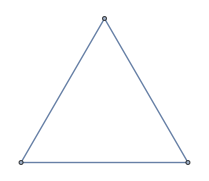

```mathematica
AdjacencyGraph[ndtriangle]
```

```mathematica
Δ=graphToNet[AdjacencyGraph[ndtriangle],{NN,1}];
```

```mathematica
tmpall=netEvolve[Δ,1000 NN];
tmp2=netEvolve[Δ,2,1000 NN];
tmp1=netEvolve[Δ,1,1000 NN];
```

```mathematica
tmpall=Transpose[Table[Length/@tmpall[[i]][[All,1]],{i,Length[tmpall]}]];
tmp2=Transpose[Table[Length/@tmp2[[i]][[All,1]],{i,Length[tmp2]}]];
tmp1=Transpose[Table[Length/@tmp1[[i]][[All,1]],{i,Length[tmp1]}]];
```

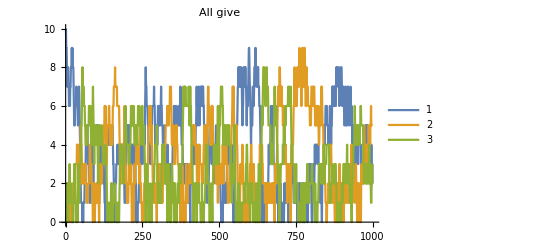

```mathematica
ListLinePlot[tmpall[[All,1;;1000]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"All give"]
```

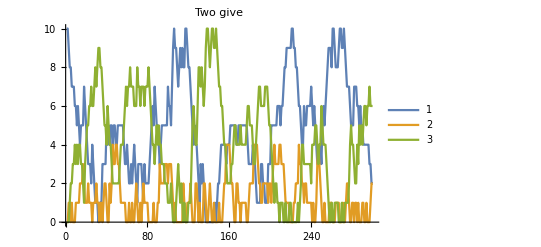

```mathematica
ListLinePlot[tmp2[[All,1;;300]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"Two give"]
```

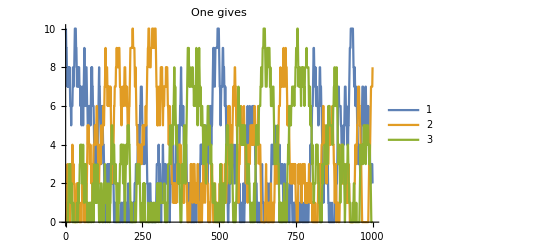

```mathematica
ListLinePlot[tmp1[[All,1;;1000]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"One gives"]
```

#### Averages

```mathematica
lots=Table[netEvolve[Δ,1000 NN],{100}];
```

```mathematica
lots=Table[Transpose[Table[Length/@lots[[j]][[i]][[All,1]],{i,Length[lots[[j]]]}]],{j,Length[lots]}];
```

```mathematica
lotsmd=Table[Table[Around[Transpose[lots[[All,n]]][[i]]],{n,3}],{i,1,1000NN,100}];
```

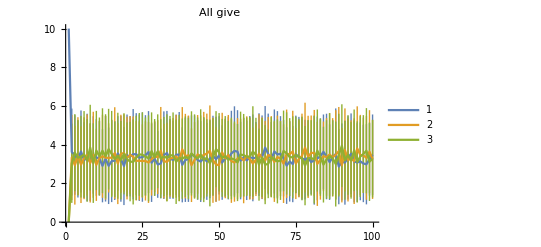

```mathematica
ListLinePlot[Transpose[lotsmd],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"All give"]
```

```mathematica
lots2=Table[netEvolve[Δ,2,1000 NN],{100}];
```

```mathematica
lots2=Table[Transpose[Table[Length/@lots2[[j]][[i]][[All,1]],{i,Length[lots2[[j]]]}]],{j,Length[lots2]}];
```

```mathematica
lotsmd=Table[Table[Around[Transpose[lots2[[All,n]]][[i]]],{n,3}],{i,1,1000NN,100}];
```

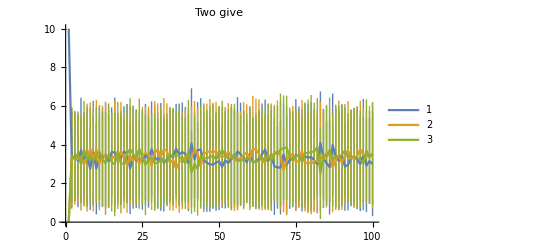

```mathematica
ListLinePlot[Transpose[lotsmd],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"Two give
"]
```

```mathematica
lots1=Table[netEvolve[Δ,1,1000 NN],{100}];
```

```mathematica
lots1=Table[Transpose[Table[Length/@lots1[[j]][[i]][[All,1]],{i,Length[lots1[[j]]]}]],{j,Length[lots1]}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,3}],{i,1,1000NN,100}];
```

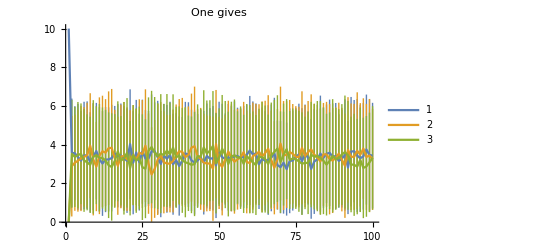

```mathematica
ListLinePlot[Transpose[lots1md],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"One gives"]
```

### 5 nodes

```mathematica
five={{0,1,0,0,0},{1,0,1,1,0},{0,1,0,1,0},{0,1,1,0,1},{0,0,0,1,0}};
```

```mathematica
M=Length[five]
```

5

```mathematica
NN=10;
```

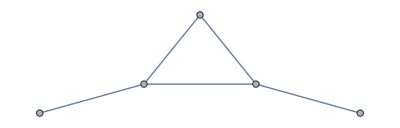

```mathematica
AdjacencyGraph[five]
```

```mathematica
five=graphToNet[AdjacencyGraph[five],{NN,5}];
```

```mathematica
tmpall=netEvolve[five,1000 NN];
tmp3=netEvolve[five,3,1000 NN];
tmp1=netEvolve[five,1,1000 NN];
```

```mathematica
tmpall=Transpose[Table[Length/@tmpall[[i]][[All,1]],{i,Length[tmpall]}]];
tmp3=Transpose[Table[Length/@tmp3[[i]][[All,1]],{i,Length[tmp3]}]];
tmp1=Transpose[Table[Length/@tmp1[[i]][[All,1]],{i,Length[tmp1]}]];
```

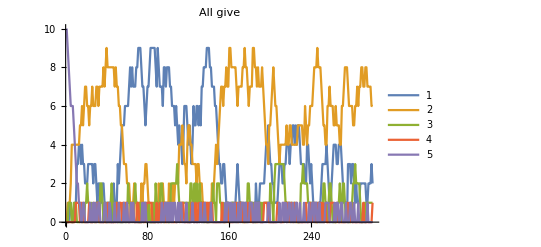

```mathematica
ListLinePlot[tmpall[[All,1;;300]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"All give"]
```

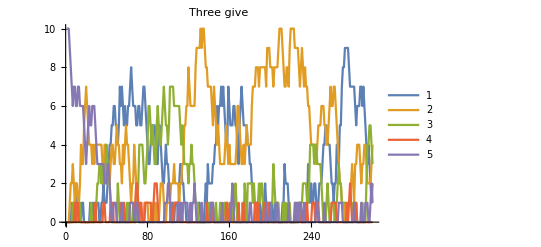

```mathematica
ListLinePlot[tmp3[[All,1;;300]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"Three give"]
```

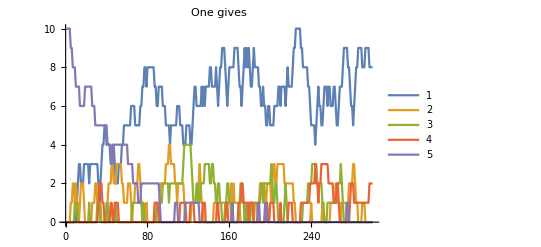

```mathematica
ListLinePlot[tmp1[[All,1;;300]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"One gives"]
```

#### Averages

```mathematica
lots=Table[netEvolve[five,1000 NN],{100}];
```

```mathematica
lots=Table[Transpose[Table[Length/@lots[[j]][[i]][[All,1]],{i,Length[lots[[j]]]}]],{j,Length[lots]}];
```

```mathematica
lotsmd=Table[Table[Around[Transpose[lots[[All,n]]][[i]]],{n,5}],{i,1,1000NN,100}];
```

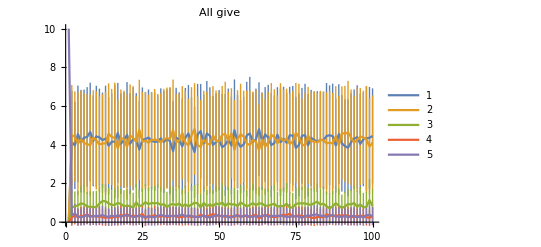

```mathematica
ListLinePlot[Transpose[lotsmd],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"All give"]
```

```mathematica
lots3=Table[netEvolve[five,3,1000 NN],{100}];
```

```mathematica
lots3=Table[Transpose[Table[Length/@lots3[[j]][[i]][[All,1]],{i,Length[lots3[[j]]]}]],{j,Length[lots3]}];
```

```mathematica
lots3md=Table[Table[Around[Transpose[lots3[[All,n]]][[i]]],{n,5}],{i,1,1000NN,100}];
```

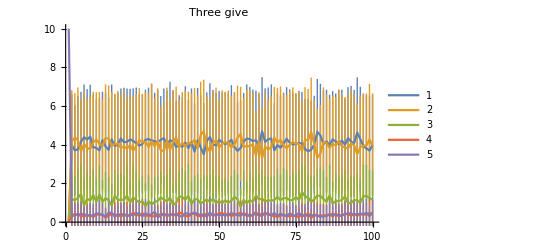

```mathematica
ListLinePlot[Transpose[lots3md],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"Three give"]
```

```mathematica
lots1=Table[netEvolve[five,1,1000 NN],{100}];
```

```mathematica
lots1=Table[Transpose[Table[Length/@lots1[[j]][[i]][[All,1]],{i,Length[lots1[[j]]]}]],{j,Length[lots1]}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,5}],{i,1,1000NN,100}];
```

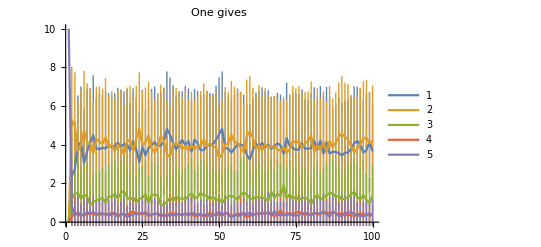

```mathematica
ListLinePlot[Transpose[lots1md],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"One gives"]
```

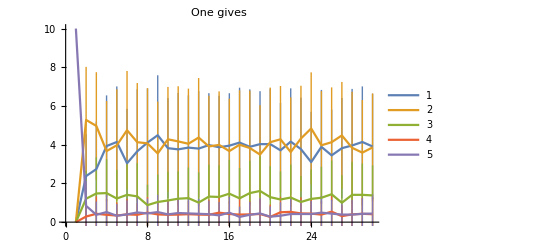

```mathematica
ListLinePlot[Transpose[lots1md[[1;;30]]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"One gives"]
```